```mathematica
Krivulje II.reda
```

Krivulja drugeg drugega reda je je vsaka množica ravninskih točk, ki ustrezajo enačbi drugega reda:
 Ax^2 + Bxy+ Cy^2 + Dx + Ey + F = 0
Glavne krivulje drugega reda so krožnica, elipsa, hiperbola in parabola.

```mathematica
Krožnica
```

Krožnica je množica ravninskih točk, ki so enako oddaljene od danega središča (S). Oddaljenost poljubne točke od središča imenujemo polmer ali radij krožnice (r).


ENAČBA KROŽNICE:
x^2 + y^2 = r^2 (enačba krožnice v sredični legi)
(x - (p))^2 + (y - (q))^2 = r^2 (enačba krožnice v premaknjeni legi)
Primera:

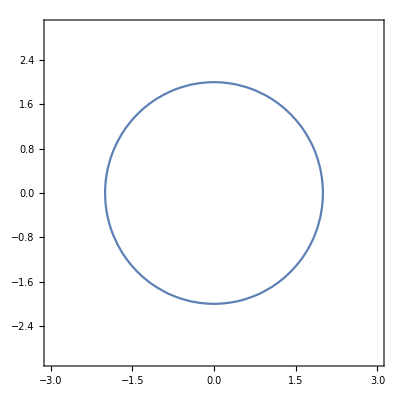

```mathematica
krožnica1 = ContourPlot[x^2 + y^2 == 4, {x, -3,3},{y,-3,3}]
```

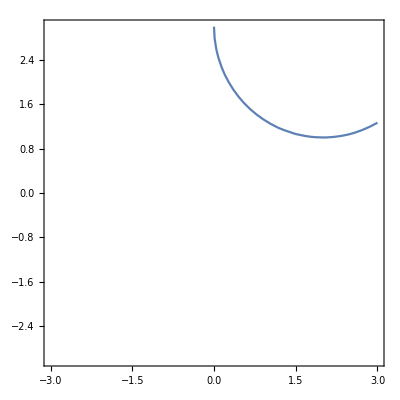

```mathematica
krožnica2 = ContourPlot[(x-2)^2 + (y - 3)^2 == 4, {x, -3,3},{y,-3,3}]
```

```mathematica
Elipsa
```

Elipsa je množica ravninskih točk, za katere je vsota razdalj do dveh danih točk konstantna. Ti dve točki imenujemo gorišči elipse (G1 in G2).

Elipsa ima dve simetrijski osi (simetrali). Njuno presečišče je središče elipse (S). Točke, kjer simetrali sekata elipso, so temena elipse (T1, T2, T3, T4).
Razdalja od središča do bolj oddaljenega temena se imenuje velika polos elipse (ponavadi jo označimo a), razdalja od središča do manj oddaljenega temena pa se imenuje mala polos elipse (ponavadi jo označimo b).
Gorišči elipse ležita vedno na veliki osi. Razdalja od središča do gorišča se imenuje linearna ekscentričnost elipse (e).
Razmerje med linearnano ekscentričnostjo in veliko polosjo imenujemo numerična ekscentričnost elipse (ε). Numerična ekscentričnost leži vedno na intervalu (0, 1) in nam pove, kakšne oblike je elipsa. Če je ε blizu 0, je elipsa po obliki podobna krogu; če je ε blizu 1, pa je elipsa zelo razpotegnjena (podolgovata).

Enačba elipse:
x^2/a^2+y^2/b^2 = 1
Primera:
če je a > b, potem velja, da je e = √(a^2 - b^2) in  ε = e/a

```mathematica
elipsa1 = ContourPlot[x^2/9+y^2/4==1 ,{x,-5,5},{y,-5,5}]
```

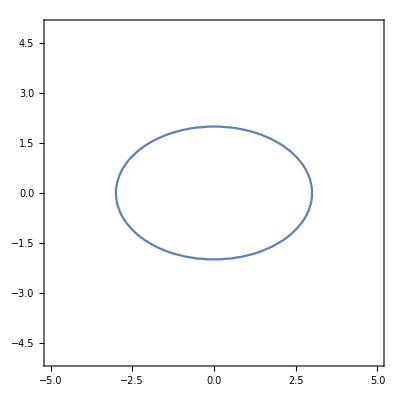

Če  je pa b > a, velja e = √(b^2 -a^2) in ε  = e/b

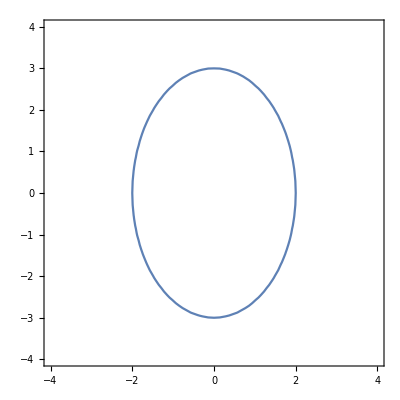

```mathematica
elipsa2 = ContourPlot[x^2/4+y^2/9== 1 , {x, -4,4}, {y,-4,4}]
```

Formula, če (x-p)^2/a^2 + (y - q)^2/b^2 = 1, če je elipsa v premaknjeni legi.

```mathematica
Hiperbola
```

Hiperbola je množica ravninskih točk, za katere je absolutna vrednost razlike razdalj do dveh danih točk konstantna. Ti dve točki imenujemo gorišči hiperbole (G1 in G2).

Hiperbola ima dve simetrijski osi (simetrali). Njuno presečišče je središče hiperbole (S). Točki, kjer ena od simetral seka hiperbolo, sta temeni hiperbole (T1 in T2). Druga simetrala ne seka hiperbole.
Razdalja od središča do temena se imenuje polos (tudi realna polos) hiperbole - ponavadi jo označimo a.
Gorišči hiperbole ležita vedno na isti osi kot temeni. Razdalja od središča do gorišča se imenuje linearna ekscentričnost hiperbole (e).
Razmerje med linearnano ekscentričnostjo in realno polosjo imenujemo numerična ekscentričnost hiperbole (ε). Numerična ekscentričnost je vedno večja od 1 in nam pove, kakšne oblike je hiperbola.
Hiperbola ima dve asimptoti: ko se oddaljujemo od izhodišča koordinatnega sistema, se hiperbola približuje tema dvema premicama. Pri risanju asimptot si pomagamo s pravokotnim okvirjem, ki ga določata realna polos a in število b, ki ga imenujemo imaginarna polos in je določeno z enačbo:
  a^2 + b^2 = e^2
  
  Enačba hiperbole:
  x^2/a^2 - y^2/b^2 = 1
  
  ločimo dva tipa hiperbol:
  1. Gorišči ležita na abscisni osi, prav tako tudi obe temeni.

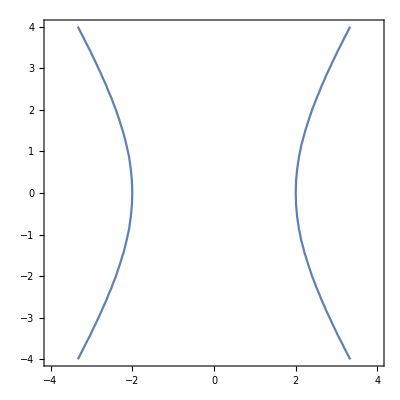

```mathematica
hiperbola1 = ContourPlot[x^2/4-y^2/9== 1 , {x, -4,4}, {y,-4,4}]
```

2.Gorišči ležita na ordinatni osi, prav tako tudi obe temeni.

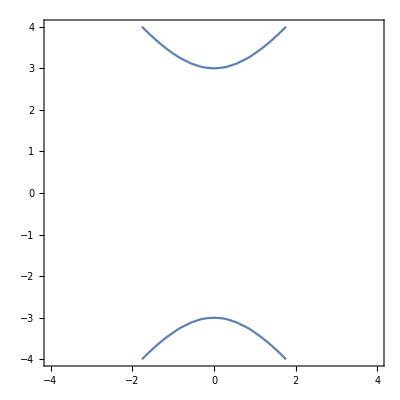

```mathematica
hiperbola2 = ContourPlot[x^2/4-y^2/9== -1 , {x, -4,4}, {y,-4,4}]
```

```mathematica
Parabola
```

Parabola je množica ravninskih točk, ki so enako oddaljene od dane premice vodnice (v) in od dane točke, ki jo imenujemo gorišče (G).

Parabola ima eno simetrijsko os (simetralo). Točko, kjer os seka parabolo, imenujemo teme parabole (T).
Razdaljo med goriščem in vodnico imenujemo parameter parabole (p).

Enačba parabole:
y^2= 2px

 Ločimo 4. tipe parabol:
1. Prvi tip ima enačbo y^2 = 2px

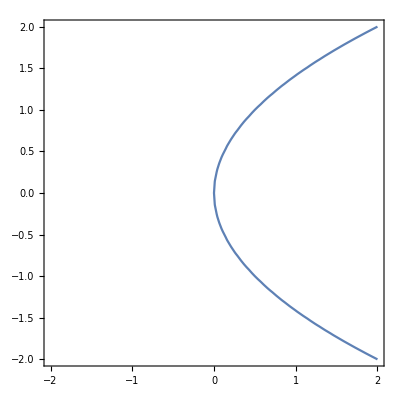

```mathematica
parabola1 = ContourPlot[y^2 == 2x, {x,-2,2}, {y,-2,2}]
```

2.  Parabola drugega tipa ima enačbo: y^2 = −2px

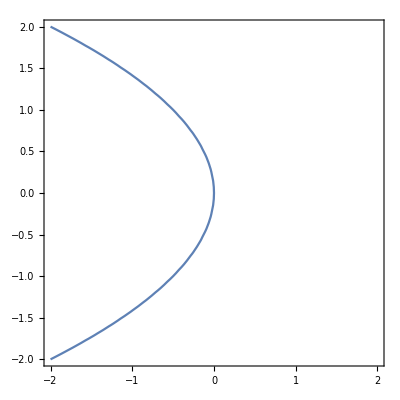

```mathematica
parabola2 = ContourPlot[y^2 == -2x, {x,-2,2}, {y,-2,2}]
```

3. Parabola tretjega tipa ima enačbo: x^2 = 2py

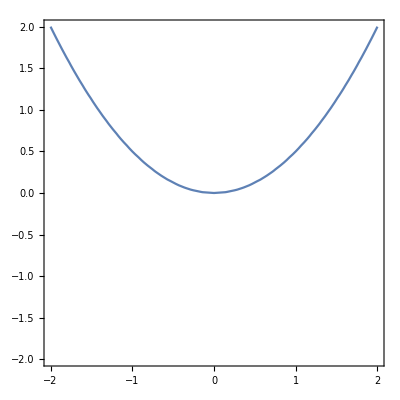

```mathematica
parabola3 = ContourPlot[x^2 == 2y, {x,-2,2}, {y,-2,2}]
```

4.Parabola četrtega tipa ima enačbo: x^2 = −2py

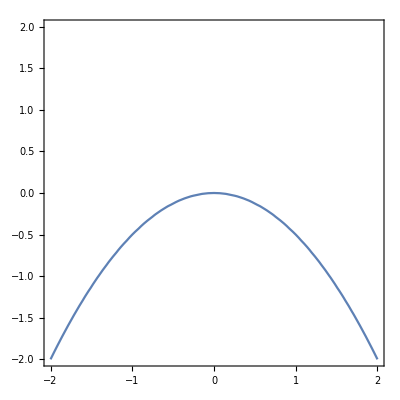

```mathematica
parabola4 = ContourPlot[x^2 == -2y, {x,-2,2}, {y,-2,2}]
```

1.Naloga:
                        1.1 Zapiši enačbo krožnice, ki ima središče S(5,−2) in poteka skozi točko T(−1,6), ter jo nariši.

```mathematica
g[x_,y_] := (x-5)^2 + (y+2)^2
```

```mathematica
g[-1,6]
```

100

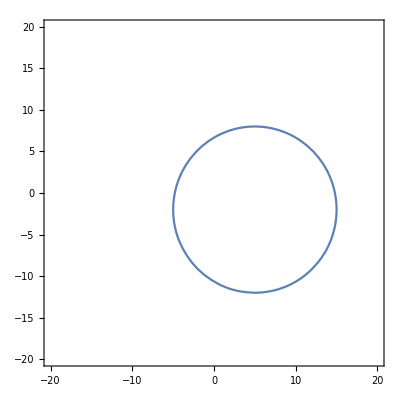

```mathematica
grafkrožnice  = ContourPlot[(x-5)^2 + (y+2)^2 == 100, {x,-20,20}, {y, -20,20}]
```

2.Naloga: 
                      2.1 Nariši elipsi:
 a)  x^2+9 y^2−2x+54y+73=0
 b) 2 x^2+8 y^2+4x−16y−22=0

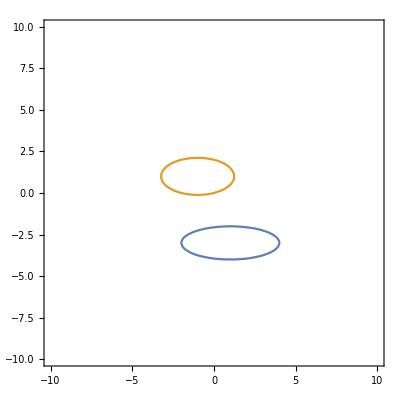

```mathematica
graf = ContourPlot[{x^2 + 9*y^2 - 2x + 54y + 73 == 0,2*x^2 + 8y^2 +4*x-16*y == 0}  , {x, -10,10}, {y,-10,10}]
```

3. Naloga:
                       3.1 Ali je premica tangenta parabole,in če je jo nariši:
 y^2 = 3x
 x - 4y +12 = 0

```mathematica
sistemenacb = Solve[{y^2 == 3x, x -4y +12 == 0}]
```

{{x→12,y→6}}

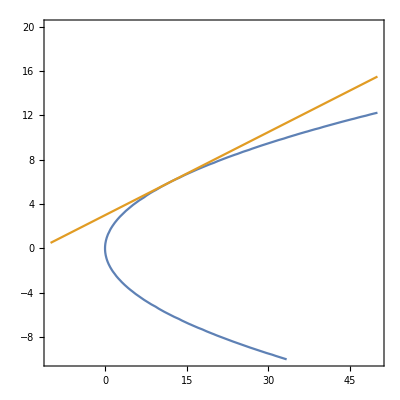

```mathematica
graf = ContourPlot[{y^2 == 3x, x -4y +12 == 0}, {x,-10,50}, {y,-10,20}]
```

4.Naloga:
                     4.1Določi presečišče krožnice in elipse:
x^2+ y^2 =  8
x^2+ 3 y^2 = 12

```mathematica
enačba = Solve[{x^2 + y^2 == 8, x^2 + 3*y^2 == 12}]
```

{{x→-√6,y→-√2},{x→-√6,y→√2},{x→√6,y→-√2},{x→√6,y→√2}}

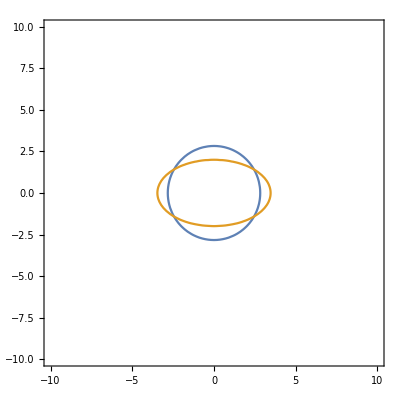

```mathematica
graf1 = ContourPlot[{x^2 + y^2 == 8, x^2 + 3*y^2 == 12}, {x,-10,10}, {y,-10,10}]
```